# Plotting Solutions of ODEs

Informal Theorem
An ODE y'=f(t,y(t)) with an initial condition y'(t_0)=y_0 has a unique solution on some interval around t_0 if f:ℝ×ℝ^n→ℝ^n is smooth.

I will plot a solution to the Rosseler ODE system 
	-Graphics-	
to demonstrate how to compute and plot  a solution. For more information see the wikipedia page 
https://en.wikipedia.org/wiki/R%C3%B6ssler_attractor

```mathematica
{x->0.007026204834100129,y->-0.035131024170500645,z->0.035131024170500645}
```

```mathematica
Clear[y,t,f,a,b,c,ySol]
{a,b,c}={0.2,0.2,5.7};
t0=1.2; TMax=24;
y0={1.1,1.2,5.4};
f[t_,{x_,y_,z_}]:= {-y-z,x+ a y, b  + z(x-c)}
ySol = NDSolveValue[{y'[t]==f[t,y[t]],y[t0]==y0},y,{t,t0, TMax}];
ParametricPlot3D[ySol[t],{t,t0,TMax},PlotRange->All,PlotPoints->2123,
PlotStyle->Thin]
```

-Graphics3D-

The solution is a 3D curve.  You can get pieces of the curve using the [[ ]] part command shown below.

```mathematica
vec={1.2,3.4,5.6,7.8};
vec⟦1⟧
vec[[{3,2}]]
```

1.2

{5.6,3.4}

Here is it in action

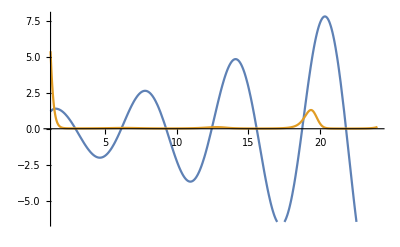

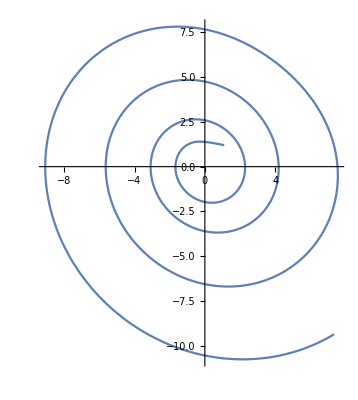

```mathematica
Plot[{ySol[t][[2]],ySol[t][[3]]},{t,t0,TMax}]
ParametricPlot[ySol[t][[{1,2}]],{t,t0,TMax}]
```

-Graphics3D-

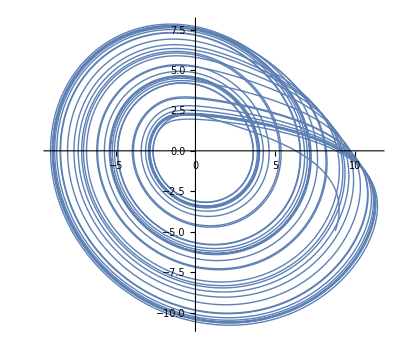

```mathematica
Clear[y,t,f,a,b,c]
{a,b,c}={0.2,0.2,5.7};
t0=1.2; TMax=234;
y0={1,2.0021,2.9};
f[t_,{x_,y_,z_}]:= {-y-z,x+ a y, b  + z(x-c)}
ySol = NDSolveValue[{y'[t]==f[t,y[t]],y[t0]==y0},y,{t,0, TMax}];
ParametricPlot3D[ySol[t],{t,0,TMax},PlotRange->All,PlotPoints->2123,
PlotStyle->Thin]
ParametricPlot[ySol[t][[{1,2}]],{t,0,TMax},PlotRange->All,PlotPoints->2123,
PlotStyle->Thin]
```

There are lots of ways to plot solutions in 3D

```mathematica
ySol[1.205]
```

{0.975155,2.00694,2.93113}

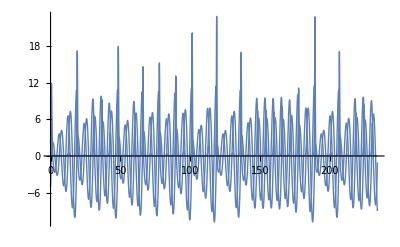

```mathematica
Plot[ySol[t],{t,0,TMax},PlotRange->All,PlotPoints->2123,
PlotStyle->Thin]
```

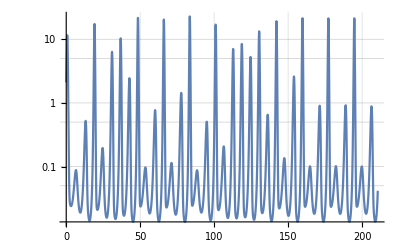

```mathematica
LogPlot[ySol[t][[3]],{t,0,0.9TMax},PlotRange->All,
GridLines->Automatic]
```

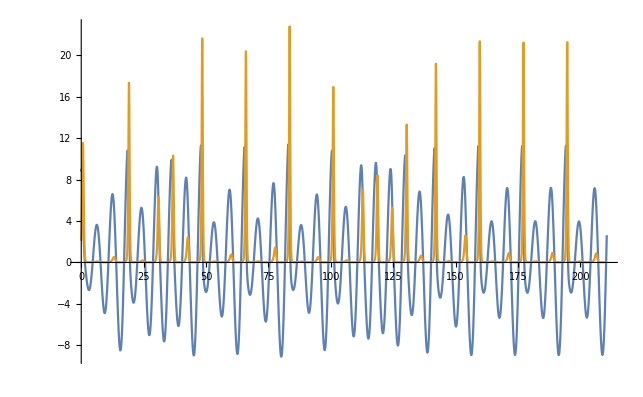

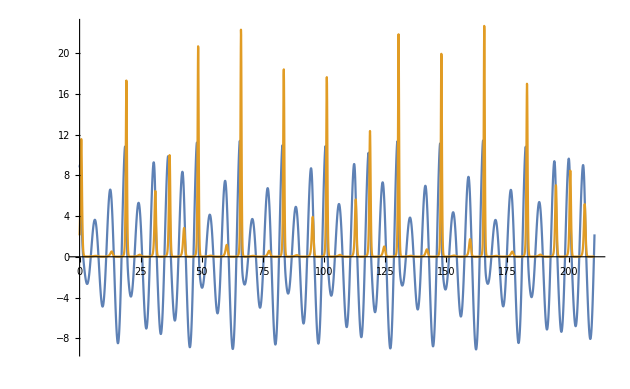

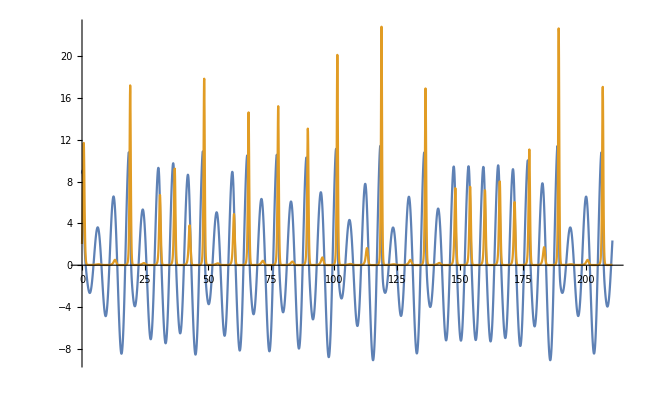

```mathematica
Plot[{ySol[t][[1]],ySol[t][[3]]},{t,0,0.9TMax},PlotRange->All]
```

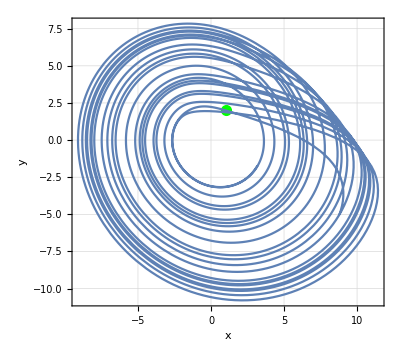

```mathematica
x=2;
ParametricPlot[ySol[t]⟦{1,2}⟧,
{t,0,TMax},PlotRange->All,
Prolog->{Green,PointSize[0.02],Point[y0⟦{1,2}⟧]},
Frame->True,
GridLines->Automatic,
FrameStyle->Directive[Thick,Purple],
AxesStyle->Directive[Thick,Dashed,Magenta],
FrameLabel->{"x","y"}]
```

```mathematica
ySol[12]
```

{5.69984,-3.36871,0.121335}